```mathematica
IntegerDigits[RandomInteger[100],2]
```

```mathematica
FromDigits[{1,0,0,1,1,0,1},2]
```

77

```mathematica
oneap[77]
```

77

```mathematica
oneap[15]
```

15

```mathematica
Table[oneap[i],{i,1,100}]
```

{1,1,3,1,5,3,7,1,9,5,11,3,13,7,15,1,17,9,19,5,21,11,23,3,25,13,27,7,29,15,31,1,33,17,35,9,37,19,39,5,41,21,43,11,45,23,47,3,49,25,51,13,53,27,55,7,57,29,59,15,61,31,63,1,65,33,67,17,69,35,71,9,73,37,75,19,77,39,79,5,81,41,83,21,85,43,87,11,89,45,91,23,93,47,95,3,97,49,99,25}

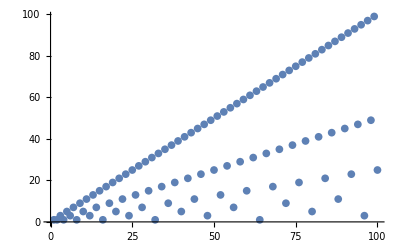

```mathematica
ListPlot[%]
```

```mathematica
FromDigits[Flatten[Table[{1,0},{i,1,10}]],2]
```

```mathematica
oneap[699050]
```

```mathematica
IntegerDigits[349525,2]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}

```mathematica
ArrayPlot[CellularAutomaton[124,{IntegerDigits[699050,2],0},100]]
```

-Graphics-

```mathematica
oneap[x_]:=FromDigits[CellularAutomaton[124,{IntegerDigits[x,2],0},0][[1]],2]
```

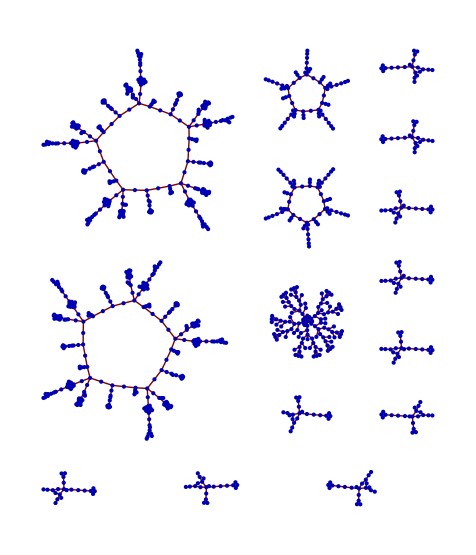

```mathematica
GraphPlot[#->CellularAutomaton[110,#]&/@Tuples[{0,1},10]]
```

```mathematica
Mod[p+r+p q+p q r,2]
```

```mathematica
Table[Mod[#[[1]]+#[[1]] #[[2]]+#[[3]]+#[[1]] #[[2]] #[[3]],2]&@Take[{0,0,1,0,0,1,1,0,1,0,0},{n,n+3}],{n,1,8}]
```

{1,0,1,1,1,0,0,0}

{1,1,0,1}

```mathematica
CellularAutomaton[124,{IntegerDigits[17,2],0},1][[2]]
```

{1,1,0,0,1,1}

```mathematica
IntegerDigits[17,2]
```

{1,0,0,0,1}

```mathematica
Map[f,Table[Take[{0,1,0,0,0,1,0,0},{i,i+2}],{i,1,6}]]
```

{1,1,0,0,1,1}

```mathematica
Clear[f]
```

```mathematica
f[{p_,q_,r_}]:=Mod[p+q+p q+p q r,2]
```

```mathematica
f2[x_]:=makeodd[FromDigits[CellularAutomaton[124,{IntegerDigits[x,2],0},1][[2]],2]]
```

```mathematica
makeodd[n_]:=Block[{m=n},While[EvenQ[m],m=m/2];m]
```

```mathematica
makeodd[2789852222]
```

```mathematica
1453 2^5
```

```mathematica
makeodd[46496]
```

1453

```mathematica
FactorInteger[2789852222/2]
```

{{1394926111,1}}

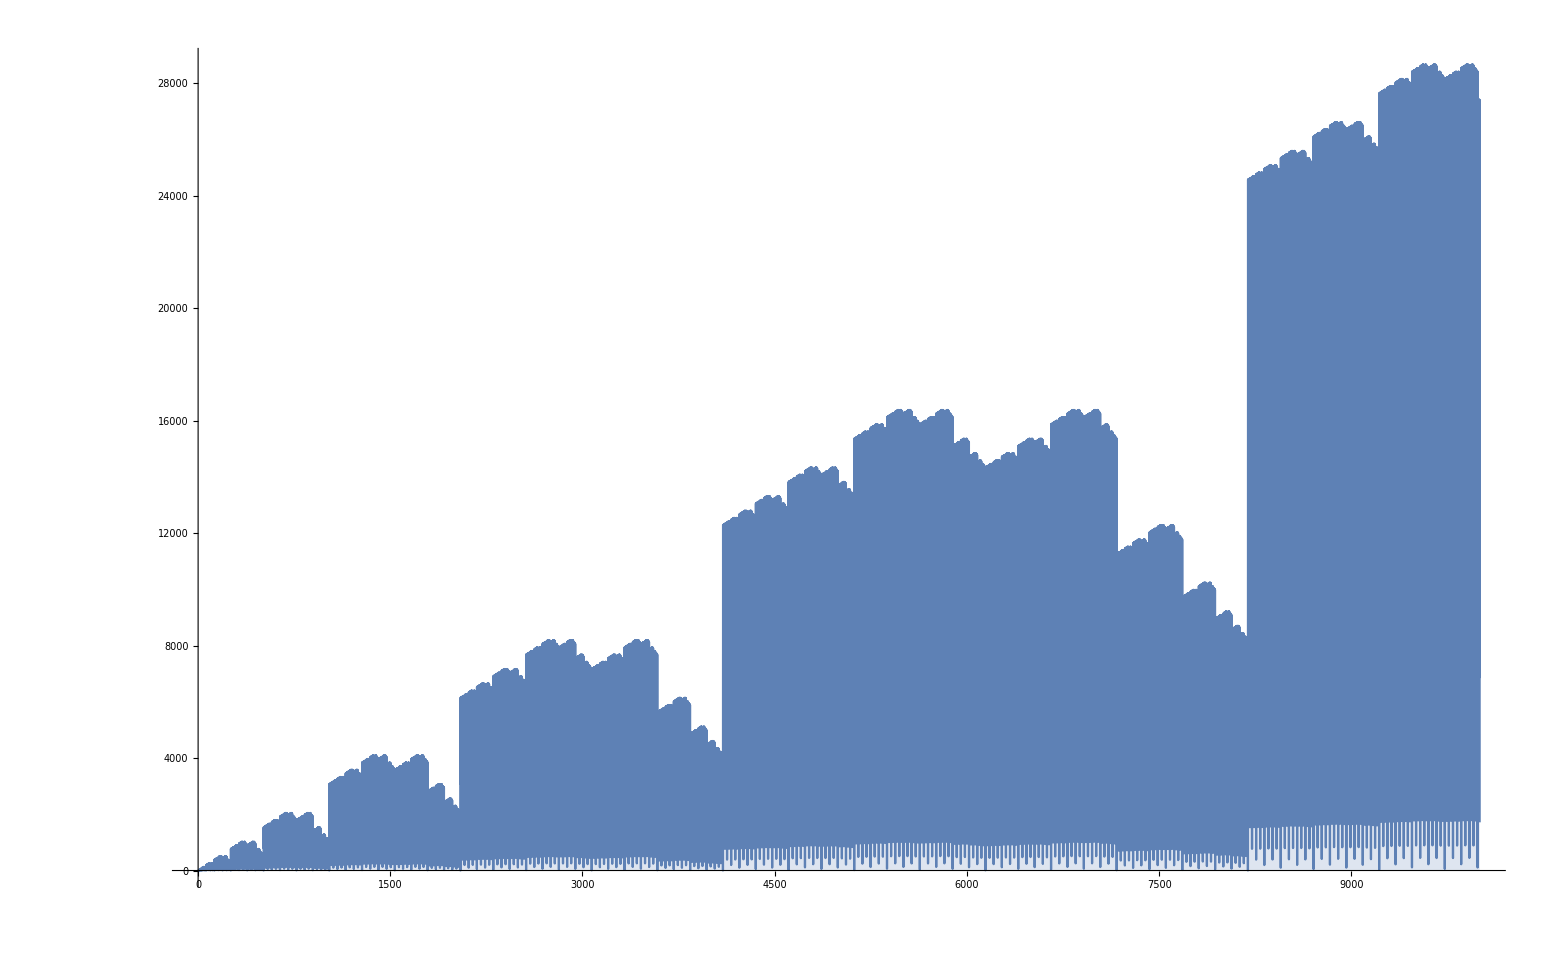

```mathematica
DiscretePlot[f2[i],{i,1,10000}]
```

```mathematica
todec[n_]:=(n/(2^Length[IntegerDigits[n,2]]-1))
```

```mathematica
IntegerDigits[2356,2]
```

{1,0,0,1,0,0,1,1,0,1,0,0}

```mathematica
RealDigits[todec[2356],2]
```

{{{1,0,0,1,0,0,1,1,0,1,0,0}},0}

```mathematica
toint[d_]:=FromDigits[RealDigits[d,2][[1,1]],2]
```

```mathematica
toint[todec[2356]]
```

2356

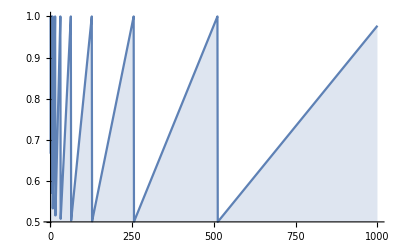

```mathematica
DiscretePlot[todec[i],{i,1,1000}]
```

```mathematica
Clear[j]
```

```mathematica
todec[f2[toint[32/63]]]
```

1

```mathematica
tflist=Sort[Select[Table[todec[i],{i,1,1000000}],#<1&]];
```

```mathematica
ttlist=Monitor[Table[{h,todec[f2[toint[h]]]},{h,tflist}],h];
```

```mathematica
ListPlot[ttlist]
```

-Graphics-

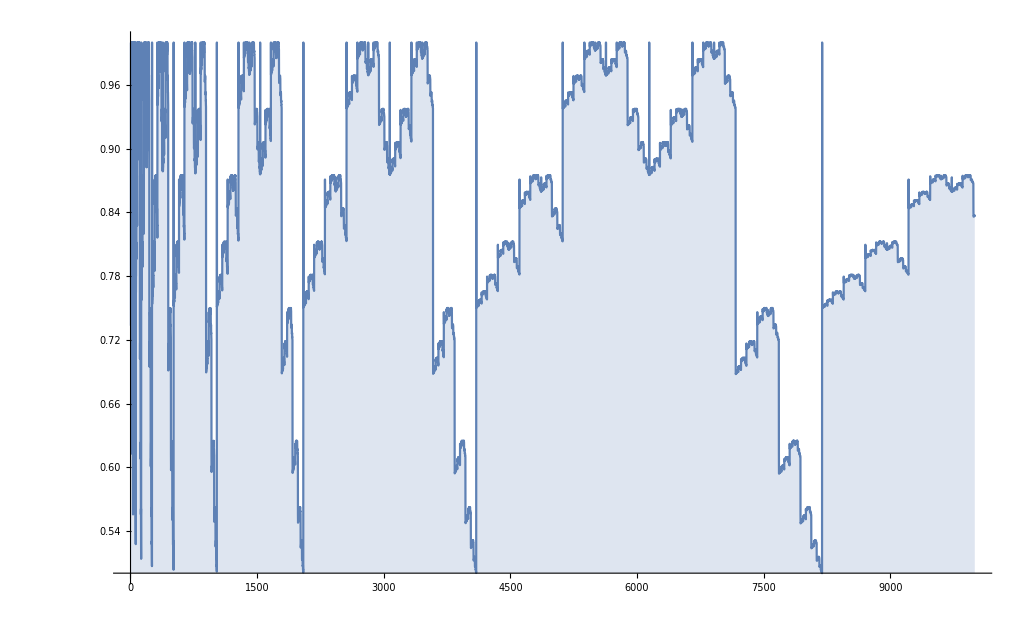

```mathematica
DiscretePlot[todec[f2[toint[i]]],{i,1,10000}]
```